```mathematica
SetDirectory["~/mthesis/graphanalysis"]
data = Import["in-out-degree"];
in = data⟦All,1⟧;
out = data⟦All,2⟧;
total = in+out;
```

/home/remco/Thesis/graphanalysis

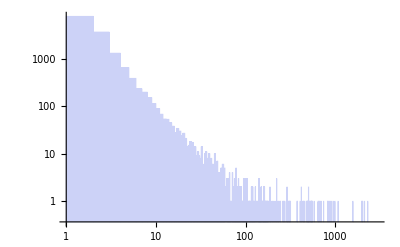

```mathematica
Histogram[in+1,{Min[in],Max[in],1},ScalingFunctions->{"Log","Log"}]
```

```mathematica
Max[in]
```

2985

```mathematica
FindDistributionParameters[in+1,ParetoDistribution[k,a]]
```

{k→1.,a→1.4917}

```mathematica
BinCounts[in,{0,1000, 1}]
```

{7798,3666,1311,651,386,232,198,151,114,89,68,54,53,45,38,28,34,30,24,27,21,14,15,18,17,14,14,9,11,9,8,14,5,6,10,11,8,3,10,6,8,6,6,4,10,6,6,7,3,4,2,3,5,5,6,6,3,5,0,2,0,3,3,1,2,4,1,1,0,1,4,1,2,1,3,2,1,5,1,1,2,2,3,2,1,2,2,0,2,0,1,1,1,1,3,2,3,3,2,3,2,1,3,1,1,0,0,1,1,1,1,1,0,1,0,2,2,2,0,2,1,0,1,1,1,0,0,2,0,1,0,1,0,0,1,0,0,1,1,0,3,1,1,2,1,1,1,0,2,1,0,0,1,0,1,1,1,1,2,0,1,2,1,1,0,1,1,1,1,0,1,0,1,0,1,1,1,0,0,0,1,0,0,0,0,0,2,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,3,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,2,0,0,0,1,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,2,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}

```mathematica
ParetoDistribution[1, 1.5]
```

ParetoDistribution[1,1.5]

```mathematica
Plot[PDF[ParetoDistribution[0,1.5],x],{x,3,3+4},Filling->Axis]
```

ParetoDistribution::posprm: Parameter 0 at position 1 in ParetoDistribution[0, 1.5] is expected to be positive.

ParetoDistribution::posprm: Parameter 0. at position 1 in ParetoDistribution[0., 1.5] is expected to be positive.

ParetoDistribution::posprm: Parameter 0 at position 1 in ParetoDistribution[0, 1.5] is expected to be positive.

General::stop: Further output of ParetoDistribution :: posprm will be suppressed during this calculation.

-Graphics-

```mathematica
PearsonChiSquareTest[in + 1, ParetoDistribution[1,1.5]]
```

3.85752624671416×10^-98756

```mathematica
Export["histo-in.pdf",%]
```

histo-in.pdf

```mathematica
Identity[asd]
```

asd

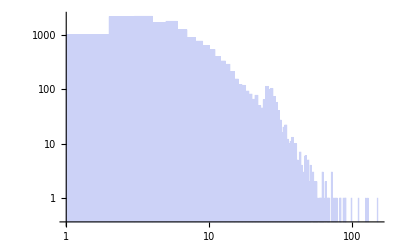

```mathematica
Histogram[out+1,{1},ScalingFunctions->{"Log","Log"}]
```

```mathematica
Export["histo-out.pdf",%]
```

histo-out.pdf

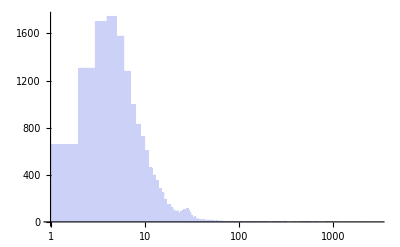

```mathematica
Histogram[total+1,{1},ScalingFunctions->{"Log"}]
```

```mathematica
Export["histo-total.pdf",%]
```

histo-total.pdf